```mathematica
Solve[{ϵ(1-p)-R0*S*V-R1*S*Ihat-ϵ*S==0,R0*S*V+ϵ*p-γ*V==0,R1*S*Ihat-Ihat==0},{S,V,Ihat}]
```

{{S→1/R1,V→(p R1 ϵ)/(-R0+R1 γ),Ihat→((-R0+R0 R1+R1 γ-R1^2 γ+p R1^2 γ) ϵ)/(R1 (R0-R1 γ))},{S→(R0+γ-√(R0^2-2 R0 γ+4 p R0 γ+γ^2))/(2 R0),V→(ϵ-(γ ϵ)/R0+(√(R0^2-2 R0 γ+4 p R0 γ+γ^2) ϵ)/R0)/(2 γ),Ihat→0},{S→(R0+γ+√(R0^2-2 R0 γ+4 p R0 γ+γ^2))/(2 R0),V→(ϵ-(γ ϵ)/R0-(√(R0^2-2 R0 γ+4 p R0 γ+γ^2) ϵ)/R0)/(2 γ),Ihat→0}}

```mathematica
R0=2
```

2

```mathematica
R1=4.5
```

4.5

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
p=0.5
```

0.5

```mathematica
γ=1
```

1

```mathematica
S=(R0+γ-√(R0^2-2 R0 γ+4 p R0 γ+γ^2))/(2 R0)
```

1/4 (3-√(1+8 p))

```mathematica
V=(ϵ-(γ ϵ)/R0+(√(R0^2-2 R0 γ+4 p R0 γ+γ^2) ϵ)/R0)/(2 γ)
```

1/2 (11/18272+(11 √(1+8 p))/18272)

```mathematica
(ϵ-(γ ϵ)/R0-(√(R0^2-2 R0 γ+4 p R0 γ+γ^2) ϵ)/R0)/(2 γ)
```

-0.000372065

```mathematica
(p R1 ϵ)/(-R0+R1 γ)
```

0.00108363

```mathematica
(R0+γ+√(R0^2-2 R0 γ+4 p R0 γ+γ^2))/(2 R0)
```

1.30902

```mathematica
((-R0+R0 R1+R1 γ-R1^2 γ+p R1^2 γ) ϵ)/(R1 (R0-R1 γ))
```

-0.000147159

```mathematica
1/2 (R0 S-R0 V-γ-ϵ-√((-R0 S+R0 V+γ+ϵ)^2-4 (R0 V γ-R0 S ϵ+γ ϵ)))
```

-0.616821

```mathematica
g[p_]:=R0 S-R0 V-γ-ϵ
```

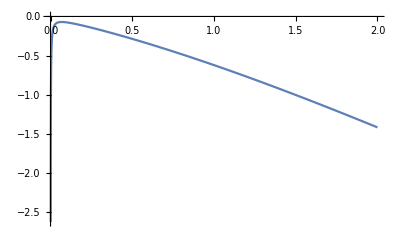

```mathematica
Plot[g[γ],{γ,0,2}]
```

```mathematica
Clear[p]
```

```mathematica
f[x_]:=R0 V γ-R0 S ϵ+γ ϵ
```

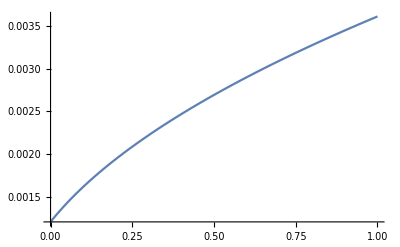

```mathematica
Plot[f[p],{p,0,1}]
```